# F 5 : Trajectoire et Thermodynamique des acides nucléiques

## 1. Marche aléatoire et Acides nucléiques (SB et DB)

#### A. Construction d’un fragment d’ADN double brin de 10 à 1000 paires de bases.

```mathematica
RandomVariate[NormalDistribution[0,5],{2,2}];
```

```mathematica
Table[RandomVariate[NormalDistribution[0,5],{1}],{x,1,10}]
```

{{4.11437},{-6.48863},{5.42535},{-2.21151},{-6.5354},{-0.276116},{-7.6512},{3.41678},{2.90221},{-7.88885}}

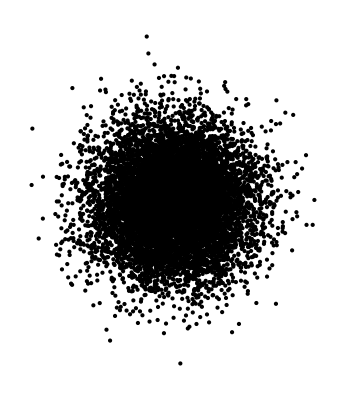

```mathematica
Graphics[{Point[RandomVariate[NormalDistribution[],{10000,2}]]}]
```

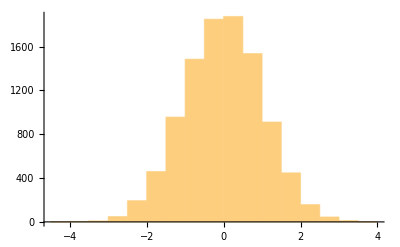

```mathematica
RandomVariate[NormalDistribution[],{10000}]//Histogram
```

```mathematica
nbp= 60;
theta[μ_,σ_,length_]:=RandomVariate[NormalDistribution[μ,σ],{length}];
theta[0Degree,5Degree,nbp]
```

{0.141437,-0.0206223,-0.180412,0.0136418,0.0172754,0.0831611,0.101941,0.0140238,-0.106287,0.029139,0.0160535,-0.0195579,-0.0752058,-0.24364,0.15717,-0.1013,-0.110254,-0.0684175,-0.111064,-0.0820181,0.0816173,-0.0581141,0.090097,-0.0618601,0.0493429,-0.114332,-0.0209023,-0.32761,-0.145537,0.039274,0.00573064,-0.0422074,-0.0773922,0.114166,-0.1559,-0.0621573,0.228789,0.0474025,-0.0340134,-0.11273,0.0426473,0.109777,0.0913692,-0.100603,-0.135088,-0.0978918,0.0211039,-0.198016,-0.16718,0.0205689,0.0288671,-0.0404604,-0.103052,-0.0901925,0.0533258,0.206217,0.0169983,0.109875,0.0312768,0.0516471}

```mathematica
thetas[μ_,σ_,length_]:=(FoldList[Plus,0,theta[μ,σ,length]]);
```

```mathematica
tiadn[μ_,σ_,length_]:=(Table[{Sin[θ],Cos[θ]},{θ,thetas[μ,σ,length]}]);
```

```mathematica
tjadn[μ_,σ_,length_]:=FoldList[Plus,{0,0},tiadn[μ,σ,length]];
```

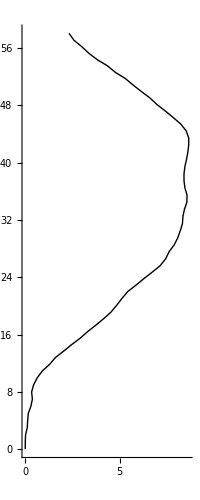

```mathematica
Show[Graphics[Line[tjadn[0Degree,5Degree,nbp]]],Axes->True]
```

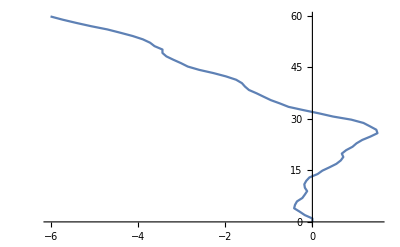

```mathematica
ListPlot[tjadn[0Degree,5Degree,nbp],Joined->True]
```

#### B. Application : Visualisation d’un petit oligonucléotide “quasiment droit”, et “courbes”

```mathematica
tjadnList[μ_,σ_,length_,imax_]:=Table[tjadn[μ,σ,length],{i,imax}];
```

{{{0,0},{0,1},{-0.0447769,1.999},{-0.105961,2.99712},{-0.223348,3.99021},{-0.231278,4.99018},{-0.20952,5.98994},{-0.146488,6.98795},{-0.154252,7.98792},{-0.0553115,8.98302},{0.0470927,9.97776},{0.341557,10.9334}},{{0,0},{0,1},{-0.198671,1.98007},{-0.44991,2.94799},{-0.60813,3.9354},{-0.953762,4.87377},{-1.17672,5.84859},{-1.51603,6.78927},{-1.87827,7.72135},{-2.25385,8.64814},{-2.56318,9.5991},{-2.80215,10.5701}}}

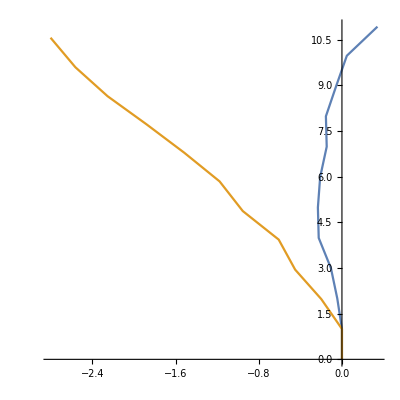

```mathematica
tjs=Table[tjadn[0Degree,5Degree,10],{i,2}]
ListPlot[tjs,AspectRatio->1.,Axes->Automatic,Joined->True]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->{{-nbp/2,nbp/2},{0,nbp}}],{σ,2Degree,10Degree},{length,2,nbp,1},{x,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,2Degree,20Degree},{length,2},{x,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,5Degree},{length,60},{x,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,2Degree,20Degree},{length,150},{x,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,4.75Degree},{length,150},{x,1,100,1}]
```

#### À partir de quelle taille peut-on raisonnablement s’attendre à des circularisations ? Discuter

Discusion de voir un cicle à partir de quelle taille ? 
On peut voir le tourne d’un brin comme une marche random dans une dimension suivant la loi uniforme, voir le lengeur comme le chemin de la marche random. 
La distance qu’on veut arriver est 2π, Esperance est 0, le lengeur de chaque pas est la valeur de σ dans le graphe de manipulate
Donc, a partir de (2π)/σ, la probablitié de voir un cicle augmente en suivant loi normal:
Probability[x>2π,x\[Distributed]NormalDistribution[0,σ]]

#### C. Construction de grands ADN

```mathematica
nbp = 10000;
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->Automatic],{σ,2Degree,10Degree},{length,100,nbp,100},{x,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],Joined->True,AspectRatio->1.,Axes->Automatic,PlotRange->{{-nbp,nbp},{-nbp,nbp}}],{σ,2Degree,10Degree},{length,100,nbp,100},{x,1,100,1}]
```

```mathematica
sqnbp=2*300 √(nbp/300)//N//IntegerPart
```

3464

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],PlotRange->{{-sqnbp,sqnbp},{-sqnbp,sqnbp}},AspectRatio->1.,Axes->Automatic,Joined->True],{σ,2Degree,10Degree},{length,100,sqnbp,100},{x,1,100,1}]
```

```mathematica
Manipulate[ListPlot[Table[tjadn[0,σ,length],{x}],PlotRange->{{-sqnbp,sqnbp},{-sqnbp,sqnbp}},AspectRatio->1.,Axes->None,Joined->True],{σ,2Degree,10Degree},{length,100,sqnbp,100},{x,1,100,1}]
```

```mathematica
Exit[]
```

## 2. Modification du pK par des interactions ioniques

#### Les acides aminés His 31 et Asp 70 dans le lysozyme T4 sont séparés par 3.5 Å et forment une paire d’ions. Si cette paire est annulée par mutagénèse dirigée (Asp70->Asn70), la stabilité de la protéine est réduite d’environ 12 à 20 kJ/mol.

#### 1./ Calculer l’énergie potentielle coulombienne entre les deux résidus chargés. On supposera que ce sont des charges ponctuelles dans un milieu de constante diélectrique ϵ = 40.

```mathematica
ϵ=40;
Subscript[N, A]=Quantity[6.02214129*10^23,"1/mole"];
Subscript[ϵ, 0]=Quantity[8.854187817620*10^-12," Coulomb^2/Netwon/metre^2"];
r=Quantity[3.5,"Å"];
EnergiePotCoul[q1_,q2_]:=(Subscript[N, A]/(4*π*ϵ*Subscript[ϵ, 0])*(q1*q2)/r)
q1=Quantity[-1.602*10^-19,"Coulomb"];
q2=Quantity[1.602*10^-19,"Coulomb"];
U=UnitConvert[EnergiePotCoul[q1,q2],"Joule/Mole"]
```

-9921.77

#### 2./ Estimer le changement de pK du résidu histidine en supposant que l’énergie de la paire d’ions se reflète intégralement dans l’enthalpie libre δG associée à la perturbation du pK. δG = 2.303*RT δpK, R=8.314 uSI, et T = 300 K.

```mathematica
R=Quantity[8.314,"Joule/K/mole"];
T=Quantity[300,"K"];
δpK[δG_]:=(δG/(2.303*R*T));
δG=Quantity[8*10^3,"Joule/mole"];
δpK[δG]
```

1.39272

#### 3./ Calculer le pK de cette histidine dans la paire d’ions (le pK normal de l’histidine est 6.0).

```mathematica
Subscript[pk, histidine]=6.0
Subscript[pk, histidine]+UnitConvert[δpK[δG]]
```

6.

6.+1.39272

```mathematica
Exit[]
```

## 3. Dérivation de l’équation de van’t Hoff (révision)

#### 0. Comment calculer des dérivées avec Mathematica

```mathematica
f[x_]:=(Sin[x])
g[x_]:=(Tan[x])
D[f[g[x]],x]
```

Cos[Tan[x]] Sec[x]^2

```mathematica
D[Log[u[x]],u[x]]
```

1/u[x]

```mathematica
D[Log[u[x]],x]
```

u'[x]/u[x]

```mathematica
D[1/T,T]
```

-1/T^2

#### 1. Lois de van’t Hoff et de Le Chatelier

#### Loi de van’t Hoff à pression constante (ou à volume constant) : l’élévation de température d’un système en équilibre maintenu à pression constante (ou à volume constant) provoque un déplacement dans le sens où la transformation est endothermique ; et vice versa.

#### Loi de Le Chatelier Une augmentation de pression dans un système en équilibre maintenu à température constante provoque une transformation dans le sens où si elle se produisait seule à pression extérieure constante et à température constante, elle serait accompagnée d’une diminution de volume.

#### 2. Exercice :

#### À partir de la loi d’action de masse et de δG° = δH° - TδS°, dériver l’équation de l’isobare de van’t Hoff : d[Log Kp]/(d T)s , p = (δH°)/T^2et montrer que l’on retrouve bien l’énoncé de la loi ci-dessus à pression constante. Expliquer comment on mesure δH° à partir de l’équation de van’t Hoff.

#### 3. Solution

Définition de l’enthalpie libre :
δG° = δH° - T δS°
(δG°)/T = (δH°)/T - δS°
En prenant la dérivée de (δG°)/T à S = constante et P = 1 atm. =cte
d[δG°/T]/(d T) = (-δH°)/T^2
Et en utilisant la loi d’action de masse :
δG° = - R T Log Kp
En remplaçant la loi d’action de masse dans l’expression précédente, on obtient l’équation de l’isobare de van’t Hoff :
d[Log Kp]/(d T) = (1/R) d[δG°/T]/(d T) = (-δH°)/RT^2
Sous la forme :
d[Log Kp] =(-δH°)/RT^2dT
On observe que si la T croît, dT > 0 et si δH° < 0 (exothermique), alors d[Log Kp] < 0 donc Kp décroît, ce qui signifie que le numérateur (partie droite de la réaction) décroît par rapport au dénominateur (partie gauche de la réaction).

On observe donc bien une évolution de la réaction dans le sens où la réaction est endothermique.

Intégration de l’équation de van’t Hoff :
Log[ Kp(T_2)/Kp(T_1) ] = -δH°/R(1/T_2-1/T_1)
δH° est obtenue par l’équation de van’t Hoff à partir de la pente de la courbe de Log Kp en fonction de 1/T
R T^2 d[Log Kp]/dT = -R d[LogKp]/d(1/T)

```mathematica
Exit[]
```

## Thermodynamique de la fusion des acides nucléiques en solution

#### Définitions :

#### Un oligonucléotide auto complémentaire est un simple brin d’ADN capable de s’auto apparier. Exemple : la séquence 5’d(AAAAATTTTT)3’ est auto complémentaire. De même 5’d(ATGCGCAT)3’. Par contre, la séquence 5’d(AAAAAGTTTTT)3’ n’est pas auto complémentaire, bien qu’elle comporte de grandes portions qui le soient. On constate facilement qu’un oligonucléotide double brin formé par l’association de simples brins auto complémentaires est palindromique, i.e. que le fragment double brin se lit de la même façon sur un brin (sens 5’ -> 3’) ou sur l’autre brin (sens 5’->3’). Ce qui est évident puisque c’est le même brin.

#### Exemples : 5’d(AAAAATTTTT)3’ et 5’d(ATGCGCAT)3’ 3’d(TTTTTAAAAA)5’ et 3’d(TACGCGTA)5’

#### Les épingles à cheveux se forment avec des oligonucléotides simples brins qui ne sont pas tout à fait palindromiques par exemple avec 5’d(AAAAAGTTTCTTTTT)3’. Dans ce qui suit on supposera que dans la limite thermodynamique, qui est celle d’un équilibre étudié au bout d’un temps infiniment long, les oligonucléotides simples brins auto complémentaires ne forment pas d’épingle à cheveux. On remarque que, pour des temps courts de mélanges, la formation d’épingle à cheveux est au contraire favorisée cinétiquement . Expliquer en quelques lignes